/home/weinhartt/Mercury/Trunk/Documentation/Images/Walls

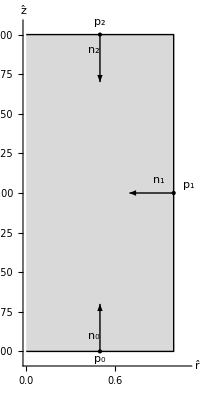

AxisymmetricWalls.png

```mathematica
SetDirectory[NotebookDirectory[]]
G3D=Graphics3D[{
Cylinder[],
Arrow[{{0,0,0},{0,0,2}}],
Text[orientation,{0,0,1.5},{-1,-1}]
},Axes->True,Ticks->{{-1,1},{-1,1},{-1,1}},AxesLabel->{x,y,z}];

G2D=Graphics[{
LightGray,Rectangle[{0,-1},{1,1}],
Black,Thick,Line[{{0,-1},{1,-1},{1,1},{0,1}}],
FontSize->14,Arrowheads[.1],
Arrow[{{.5,-1},{.5,-.7}}],Text["n_0",{.5,-.9},Right],
Arrow[{{1,0},{.7,0}}],Text["n_1",{.9,0.05},Bottom],
Arrow[{{.5,1},{.5,.7}}],Text["n_2",{.5,.9},Right],
PointSize[Large],
Point[{.5,-1}],Text[Subscript[p, 0],{.5,-1.05}],
Point[{1,0}],Text[Subscript[p, 1],{1.1,0.05}],
Point[{.5,1}],Text[Subscript[p, 2],{.5,1.05},Bottom]
},Axes->True,AxesLabel->{r̂,ẑ}];

GraphicsGrid[{{G3D,G2D}},ImageSize->Full]
Export["AxisymmetricWalls.png",%]
```

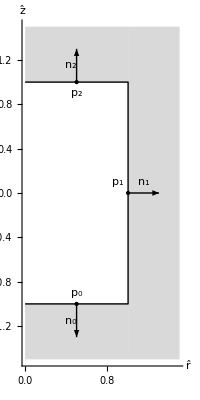

AxisymmetricWallsOuter.png

```mathematica
G2D=Graphics[{
LightGray,
Rectangle[{0,1},{1,1.5}],
Rectangle[{0,-1},{1,-1.5}],
Rectangle[{1,-1.5},{1.5,1.5}],
Black,Thick,Line[{{0,-1},{1,-1},{1,1},{0,1}}],
FontSize->14,Arrowheads[.1],
Arrow[{{.5,-1},{.5,-1.3}}],Text["n_0",{.5,-1.15},Right],
Arrow[{{1,0},{1.3,0}}],Text["n_1",{1.15,0.05},Bottom],
Arrow[{{.5,1},{.5,1.3}}],Text["n_2",{.5,1.15},Right],
PointSize[Large],
Point[{.5,-1}],Text[Subscript[p, 0],{.5,-0.9}],
Point[{1,0}],Text[Subscript[p, 1],{0.9,0.1}],
Point[{.5,1}],Text[Subscript[p, 2],{.5,0.9}]
},Axes->True,AxesLabel->{r̂,ẑ}];

GraphicsGrid[{{G3D,G2D}},ImageSize->Full]
Export["AxisymmetricWallsOuter.png",%]
```

```mathematica
G3D=Graphics3D[{
Cylinder[],
Cylinder[{{0,0,-2},{0,0,-1}},.5],
Arrow[{{0,0,0},{0,0,2}}],
Text[orientation,{0,0,1.5},{-1,-1}]
},Axes->True,Ticks->{{-1,1},{-1,1},{-1,1}},AxesLabel->{x,y,z}];

G2D=Graphics[{
LightGray,Rectangle[{0,-1},{1,1}],
Black,Thick,Line[{{0,-1},{1,-1},{1,1},{0,1}}],
FontSize->14,Arrowheads[.1],
Arrow[{{.5,-1},{.5,-.7}}],Text["n_0",{.5,-.9},Right],
Arrow[{{1,0},{.7,0}}],Text["n_1",{.9,0.05},Bottom],
Arrow[{{.5,1},{.5,.7}}],Text["n_2",{.5,.9},Right],
PointSize[Large],
Point[{.5,-1}],Text[Subscript[p, 0],{.5,-1.05}],
Point[{1,0}],Text[Subscript[p, 1],{1.1,0.05}],
Point[{.5,1}],Text[Subscript[p, 2],{.5,1.05},Bottom]
},Axes->True,AxesLabel->{r̂,ẑ}];

GraphicsGrid[{{G3D,G2D}},ImageSize->Full]
Export["AxisymmetricWallsSilo.png",%]
```

-Graphics-

AxisymmetricWallsSilo.png